```mathematica
data=Import["/home/tm/Projects/teatime_presentation/misc/files/ha_runtime_comparison.txt","Table"];
```

```mathematica
plotdata={data[[1;;28,1]],ListConvolve[{0.2,0.6,0.2},Mean@Partition[Select[data,#≠{}&][[All,2]],30]]}ᵀ;
```

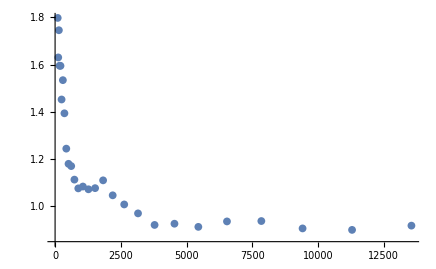

```mathematica
ListPlot@plotdata
```

```mathematica
xl=Row[{Style["Number of vertices ",FontFamily->"Latin Modern Roman",Plain,18],Style["N",FontFamily->"Latin Modern Roman",Italic,18],Style[" [m]",FontFamily->"Latin Modern Roman",Plain,18]}]
```

Number of vertices N [m]

```mathematica
yl=Row[{Style["Ratio ",FontFamily->"Latin Modern Roman",Plain,18],
DisplayForm[Row[{SubscriptBox[Style["t",FontFamily->"Latin Modern Roman",Italic,18],Style["dlib",FontFamily->"Latin Modern Roman",Plain,12]],Style["(N)",FontFamily->"Latin Modern Roman",Italic,18]}]],
Style[" / ",FontFamily->"Latin Modern Roman",Plain,18],
DisplayForm[Row[{SubscriptBox[Style["t",FontFamily->"Latin Modern Roman",Italic,18],Style["t3nsor",FontFamily->"Latin Modern Roman",Plain,12]],Style["(N)",FontFamily->"Latin Modern Roman",Italic,18]}]]}]
```

Ratio t_dlib(N) / t_t3nsor(N)

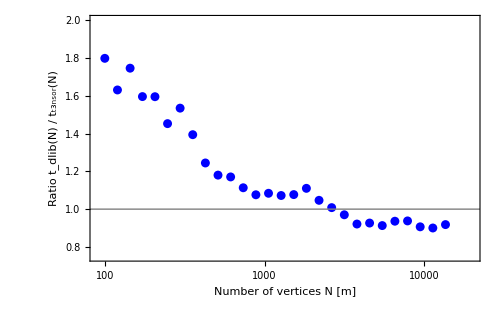

```mathematica
g=ListLogLinearPlot[
plotdata,
PlotStyle->Blue,
PlotRange->{{90,20000},{0.75,2}},
ColorFunctionScaling->False,
PlotTheme->"Scientific",
FrameStyle->Directive[Black,FontColor->Black,15,FontFamily->"Latin Modern Roman",Plain],
FrameLabel->{xl,yl},
ImageSize->{500,500./GoldenRatio},
PlotRangePadding->0,
Epilog->{Gray,Line[{{0,1},{10^5,1}}]}
]
```

```mathematica
Export["/home/tm/Projects/teatime_presentation/images/ha_runtime_comparison.png",g,ImageResolution->500];
```